```mathematica
a= 1 + I
```

1+ⅈ

```mathematica
b = 2 - I
```

2-ⅈ

```mathematica
c = a^2 /b^2
```

-8/25+(6 ⅈ)/25

```mathematica
a^2
```

2 ⅈ

```mathematica
b^2
```

3-4 ⅈ

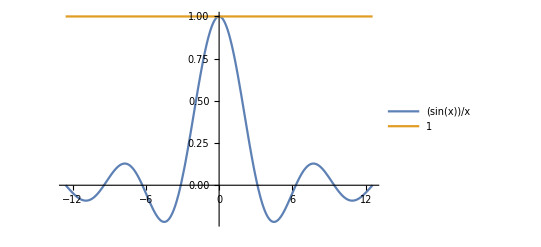

```mathematica
Plot[{Sin[x]/x,Evaluate[Limit[Sin[x]/x,x->0]]},{x,-4*Pi,4*Pi},PlotLegends->"Expressions"]
```

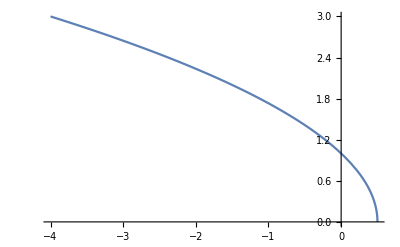

```mathematica
Plot[{Sqrt[1 - 2*x]},{x,-4,0.5}]
```

```mathematica
Cos[2 *Pi / 3]
```

-1/2

```mathematica
GTWhichAxes
```

GTWhichAxes

```mathematica
Information[GTKWhichAxes]
```

```mathematica
GTWhichAxes[]
```

GTWhichAxes[]

```mathematica
Needs["GroupTheory`"]
```

v::shdw: Symbol v appears in multiple contexts {GroupTheory`Symbols`,Global`}; definitions in context GroupTheory`Symbols` may shadow or be shadowed by other definitions.

s$::shdw: Symbol s$ appears in multiple contexts {GroupTheory`Symbols`,Global`}; definitions in context GroupTheory`Symbols` may shadow or be shadowed by other definitions.

GTWhichAxes::shdw: Symbol GTWhichAxes appears in multiple contexts {GroupTheory`Install`,Global`}; definitions in context GroupTheory`Install` may shadow or be shadowed by other definitions.

```mathematica
Needs["GroupTheory`"]
```

```mathematica
basis= {{a,0,0},{0,b,0},{c Cos[β],0,c Sin[β]}}
```

{{a,0,0},{0,b,0},{c Cos[β],0,c Sin[β]}}

```mathematica
GTSGgmat[⟨C2y,{0,1/2,1/2}⟩,⟨IC2y,{0,1/2,1/2}⟩,basis]
```

⟨IEe,{0,0,0}⟩

```mathematica
GTWhichAxes[]
```

passive definition

```mathematica
c3zp = GTGetMatrix[C3z]; c3zp // MatrixForm
```

(-1/2 | (√3)/2 | 0
-(√3)/2 | -1/2 | 0
0 | 0 | 1)

```mathematica
GTReinstallAxes["active"];
```

```mathematica
c3za = GTGetMatrix[C3z]; c3za // MatrixForm
```

(-1/2 | -(√3)/2 | 0
(√3)/2 | -1/2 | 0
0 | 0 | 1)

```mathematica
c3za . c3zp // MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
GTReinstallAxes["active"]
```

The active definition of rotation matrices is already installed.

```mathematica
GTKWhichAxes[]
```

GTKWhichAxes[]

```mathematica
GTWhichAxes[]
```

active definition

```mathematica
GTGetEulerAngles[{{-,-,0},{},{}}]
```

Syntax::tsntxi: "(√3)/2,-1/2,0" is incomplete; more input is needed.

```mathematica
GTGetEulerAngles[C3z]
```

{{0,0,(2 π)/3},1}

```mathematica
GTGetEulerAngles[C2zi]
```

Error: Input not known!

$Aborted

```mathematica
GTGetEulerAngles[C3za]
```

Error: Input not known!

$Aborted